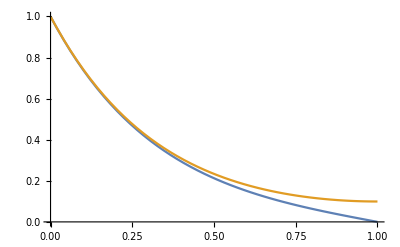

```mathematica
M = 9;
λ = √M;
T1[x_]:=(ⅇ^-λ/(ⅇ^-λ-ⅇ^λ))ⅇ^(λ x)+(-ⅇ^λ/(ⅇ^-λ-ⅇ^λ))ⅇ^(-λ x)
T2[x_]:=(ⅇ^-λ/(ⅇ^-λ+ⅇ^λ))ⅇ^(λ x)+(ⅇ^λ/(ⅇ^-λ+ⅇ^λ))ⅇ^(-λ x)
Plot[{T1[x],T2[x]},{x,0,1}]
```

```mathematica
Test[x_]=T[x]/.First@DSolve[{T''[x]-9T[x]==-100 x^2(1-x)^2,T[0]==1,T'[1]==0},T,x]//FullSimplify
```

(ⅇ^(-3 x) (1200 ⅇ^3-1157 ⅇ^6-ⅇ^(6 x) (1157+1200 ⅇ^3)+100 ⅇ^(3 x) (1+ⅇ^6) (14+9 (-1+x) x (4+3 (-1+x) x))))/(243 (1+ⅇ^6))

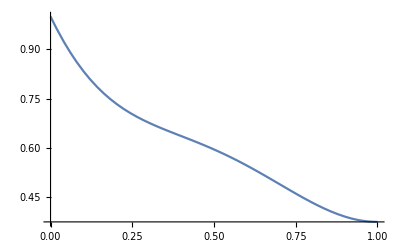

```mathematica
Plot[Test[x],{x,0,1}]
```

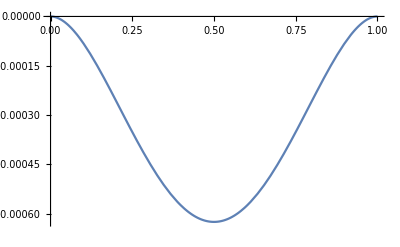

0.01

```mathematica
Plot[-100 x^2(1-x)^2*10^-4,{x,0,1}]
```

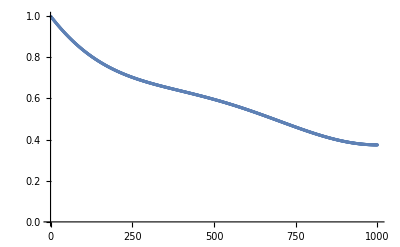

```mathematica
n = 1000;
Δx=1/n;
A = SparseArray[{{i_,i_}->-2-M Δx^2,{i_,j_}/;Abs[i-j]==1->1},{n,n}];
A[[n,n]]=-1-M Δx^2;
b = Table[-100*(i/n)^2(1-i/n)^2*Δx^2,{i,1,n}];
b[[1]]=b[[1]]-1;
sol = LinearSolve[A,b];
ListPlot[sol]
```

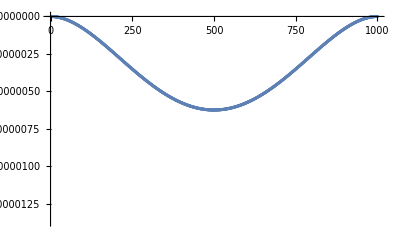

```mathematica
ListPlot[b]
```

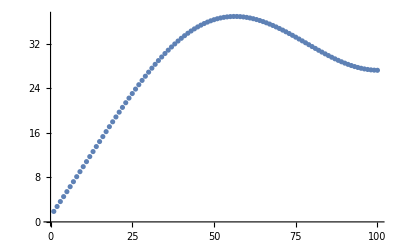

```mathematica
n = 100;
Δx=1/n;
A = SparseArray[{{i_,i_}->-2/Δx^2-M ,{i_,j_}/;Abs[i-j]==1->1/Δx^2},{n,n}];
A[[n,n]]=-1/Δx^2-M ;
b = Table[-100*(i/n)^2(1-i/n)^2,{i,1,n}];
b[[1]]=b[[1]]-1/Δx^2;
sol = LinearSolve[A,b];
ListPlot[sol]
```